## Wobbling motion in 130Ba

### band1 -> S1 band from Petrache band2 -> S1’ band from Petrache

```mathematica
ClearAll["Global`*"]
```

## Raw experimental data

```mathematica
band2=Sort[{10436.3,9283.3,8265.3,7319.3,6442.2,5647.2,4986.2,4456.2}];
band1=Sort[{11984.3,10821.3,9690.3,8574.3,7524.3,6563.3,5678.3,4884.2,4256.3,3790.3}];
band1=band1/1000;
band2=band2/1000;
spins2=Table[i,{i,11,25,2}];
spins1=Table[i,{i,10,28,2}];
```

#### create joint data with the spins and energies

```mathematica
dataB1=Table[{spins1[[i]],band1[[i]]},{i,1,Length[band1]}];
dataB2=Table[{spins2[[i]],band2[[i]]},{i,1,Length[band2]}];
(*joint data - to be used in the fitting procedure*)
dataX=Join[Insert[#,1,1]&/@dataB2,Insert[#,2,1]&/@dataB2];
dataX
```

{{1,11,4.4562},{1,13,4.9862},{1,15,5.6472},{1,17,6.4422},{1,19,7.3193},{1,21,8.2653},{1,23,9.2833},{1,25,10.4363},{2,11,4.4562},{2,13,4.9862},{2,15,5.6472},{2,17,6.4422},{2,19,7.3193},{2,21,8.2653},{2,23,9.2833},{2,25,10.4363}}

### Use the simple fit expression with the wobbling frequency and the largest moi

#### Two parameter fit

```mathematica
enB1[I_,I3_,omega_]:=1/(2*I3)*I(I+1)+omega*1/2;
enB2[I_,I3_,omega_]:=1/(2*I3)*I(I+1)+omega*3/2;
```

### Fitting procedure

```mathematica
nlm=NonlinearModelFit[dataX,{Boole[id==1]*enB1[x,a,b]+Boole[id==2]*enB2[x,a,b]},{a,b},{id,x}];
bestParameters=nlm["BestFitParameters"];
p1=Values@bestParameters[[1]];
p2=Values@bestParameters[[2]];
```

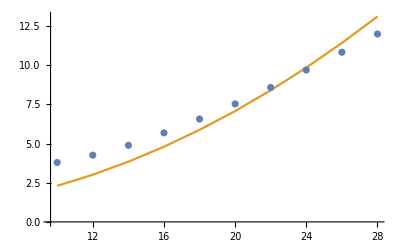

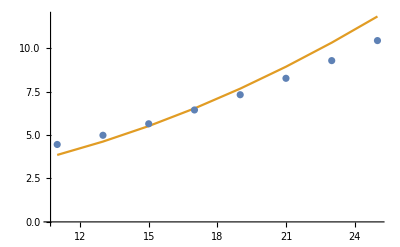

```mathematica
checkplot[data_,spins_,model_]:=ListPlot[{data,Table[{spins[[i]],model[spins[[i]],p1,p2]},{i,1,Length[spins]}]},PlotRange->All,Joined->{False,True}];
checkplot[dataB1,spins1,enB1]
checkplot[dataB2,spins2,enB2]
```